```mathematica
ClearAll["Global`*"] (* clear variables *)

(* switch off message that solar panels cannot be lower than 0 degrees *)
Off[FindMinimum::reged];
Off[FindMaximum::reged];

(* formula in directPower from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 *)

(* clear days at ~25 angle: 13/5, 19/7, 17/8 *)

(* Adjusting the solar panels x times a day
The times are evenly spread over the time the sun is up *)
year = 2016;

sunPosPrecision = 50; (* 50 is steps of half an our for the sun positions table, hopefully precise enough, at least it's fast *)

(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[i_?NumericQ,a_?NumericQ,d_]:= ( (* params: index of sunPositions table, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = sunPositions[[i]]; (* lookup sun position *)

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = -22 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)


(* parameters from urban visibility haze model *)
directPower[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
(* clear day parameters *)
(*i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;*)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

(* another function which seems similar, from http://www.solarpaneltilt.com/ *)
(*directPowerWeb[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
If[theta>Pi/2,
0,
1.35*(1/1.35)^(Sec[theta])*1000
]
)*)

calculatesunPos[d_] := ( (* params: date, initializes sunPositions table with positions of the sun for this day *)
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,d];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,d];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time, steps of 30 mins *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[d,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,sunPosPrecision} 
];
)

sumOverInterval:=Function[ (* params: solar panel angle in degrees, date, start index, end index
returns sum of solar power over the day at every time of index in the given interval *)
(* take sum of every index, hence steps of one *)
Sum[directPower[i,#1,#2],{i,#3,#4,1}]
]

angleInterval := Function[ (* params: date, start index, end index, returns optimal angle in this interval *)
(* Find for which angle of the solar panels this value is maximal,starting at 0 *)
res = FindMaximum[sumOverInterval[x,#1,#2,#3],{x,0,0,90}, AccuracyGoal->5];
{res[[1]],x /. res[[2]]}
]

dayAngles := Function[ (* params: date, number of adjustment times per day ≥ 1. returns List with optimal angles and power received with that angle over that interval, for how many adjustment times were specified *)
calculatesunPos[#1];

l = Length[sunPositions];
Table[ (* calculates indices of start and end of the interval *)
angleInterval[#1,1+Round[l*i/#2],Round[l*(i+1)/#2]]
,{i,0,#2-1}]
]

dayPower[t_] := ( (* total of power *)
sum = 0;
For[i=1,i<Length[t]+1,i++,
sum += t[[i]][[1]];
];
sum (* Total of W/m^1 received *)
)

dayPowerTable[t_] := ( (* list of power received for each angle-period *)
Table[
t[[i]][[1]],
{i,1,Length[t]}
]
)

dayAnglesTable[t_] := (
(* make list of angles *)
Table[
t[[i]][[2]],
{i,1,Length[t]}
]
)

(* find div(ision) where total W/m^m is biggest *)
totalPower[d_,v_] := ( (* params: date, division as index of sunPositions. returns total power of day, and list with two angles *)
first = angleInterval[d,1,v];
second = angleInterval[d,v+1,l];
total = first[[1]] + second[[1]];
angles = {first[[2]],second[[2]]};
{total,angles}
)

dayAngle := Function[ (* params: day of month, month, returns optimal angle for this day *)

date = DateObject[{year,#2,#1}];

position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,date];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,date];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[date,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,50}
];
(* Times 100 so the sum starts closer to the real sunUpHour, and not floors it to an integer when calculating the sum. Otherwise weird jumps in graphs appear when the sunUpHour jumps one hour *)

(* Find for which angle of the solar panels this value is maximal,starting at 50 *)

a/. FindMaximum[
Sum[directPower[h,a,date],{h,1,Length[sunPositions],1}]
,{a,50,0,90}, AccuracyGoal->5][[2]]
]

monthAngle := Function [ (* params: month, returns optimal angle for a specific month by taking the average  *)
(* Count how many days are in this month *)
days = With[{first=DateObject[{year,#1,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]] ;
Sum[dayAngle[x,#1],{x,1,days}]/days
]

 (*  NOTE for a preciser adjustment time, change step size where noted. will increase running time by as much steps are added times around three seconds *)
twoAnglesOptimal[d_] := (  (* params: date; returns in a list the date/time at which to change the angle of solar panels (besides before sunrise) to get optimal power, then the two angles of the day, then the percent increase of power compared to one setting for the whole day, then the percent increase compared to one setting if you would adjust fourteen times a day, spread evenly over the day *)
(* for two angles per day, find optimal time of angle change *)

(* some initialisation of the sunposition table *)
calculatesunPos[d];
l = Length[sunPositions];

(* steps of about one per hour is l/14 *)
(*DiscretePlot[totalPower[d,v],{v,Round[l/2],l,Round[l/12]},ImageSize -> Large]*)
t = Table[{v,totalPower[d,v]},{v,Round[l/2],Round[4 l/5],Round[l/14]}];
max = Max[t]; (* total power over the day with this setting *)
index = t[[Position[t,Max[t]][[1]][[1]]]][[1]] ;
angles = t[[Position[t,Max[t]][[1]][[1]]]][[2]][[2]] ;
(* brackets! gives index around which the highest total resides *)
(* index back to time *)
hour =(index/l)*(sunsetHour - sunriseHour)+sunriseHour ; (* the hour at which to set the solar panels second time *)
(* find percentage increase in power *)
onePower = dayAngles[d,1][[1]][[1]]; (* find power for one time *)
(* compare with percent increase in power if you'd adjust 10 times a day (not optimised) *)
tenPower= dayPower[dayAngles[d,14]];
(* return values *)
{DateObject[d,{IntegerPart[hour],Round[FractionalPart[hour]*60]}],angles,(max - onePower)/onePower * 100,(tenPower - onePower)/onePower * 100}
)

powerOverDay :=Function[d, (* param: list of angles of a day, returns a list with power outputs by index of sunPositions *)

legend=StringForm["Adjusting `` times", Length[d]];

calculatesunPos[date];

table={};

For[j=1,j< Length[d] + 1,j++,
table = Join[
table,
Table[
directPower[i,d[[j]],date]*factor,
{i,
Round[Length[sunPositions] * ((j-1)/Length[d])+1],
Round[Length[sunPositions] * (j/Length[d])]}
]
];
];

table
]

(******************************* END OF FUNCTIONS ***************************)

(* Graph for a day *)
(* date = DateObject[{2016,7,18}];
 AbsoluteTiming[DiscretePlot[sumOverDay[x,date],{x,0,90,10},ImageSize->Large,AxesLabel -> {"Solar panel angle", "Total of sun power, W/m^2"}] ] *)

(* Graph for a month *)
 (* month = 9;
days = With[{first=DateObject[{year,month,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
AbsoluteTiming[DiscretePlot[dayAngle[a,month],{a,1,days},ImageSize->Large,AxesLabel -> {"Day", "Optimal angle"}]] *)

(* Graph for this year, month average *)
(* AbsoluteTiming[DiscretePlot[monthAngle[x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}] ] *) (* ten minutes *)

(* Comparison with perpendicular to sun at noon, per month, http://www.gogreensolar.com/pages/solar-panel-tilt-calculator *)
(*greenList = {68,60,52,44,36,28,36,44,52,60,68,76};
list = Table[monthAngle[x],{x,1,12}];
ListPlot[{greenList,list},Filling-> Axis,PlotLegends-> {gogreensolar,calculations},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}]
*)

(* season values *)

(*monthSum[m_,i_,j_] := ( (* month, begin day, end day *)
Sum[
Quiet[dayAngle[x,m]],
{x,i,j}]
)
(* takes winter of [year] only. dates according to solarpaneltilt.com, summer april 18, autumn august 24, winter oct 7, spring march 5 *)
 summerSum = Quiet[monthSum[4,18,30] + monthSum[5,1,31] + monthSum[6,1,30] + monthSum[7,1,31]+ monthSum[8,1,23]];
summerDays = QuantityMagnitude[Quantity[DateDifference[{year,4,18},{year,8,23}]]]+1;
summerSum/summerDays (* 21 degrees *)

autumnSum = monthSum[8,24,31]+ monthSum[9,1,30] + monthSum[10,1,6];
autumnDays = DayCount[{year,8,24},{year,10,6}]+1;
autumnSum/autumnDays (* 49 degrees *)

 winterSum = Quiet[monthSum[10,7,31] + monthSum[11,1,30] +monthSum[12,1,31] + monthSum[1,1,31] + monthSum[2,1,29] + monthSum[3,1,4]];
winterDays = DayCount[{year,10,7},{year+1,3,4}]+1;
winterSum/winterDays  (* 73 degrees *)

springSum = Quiet[monthSum[3,5,31] + monthSum[4,1,17]];
springDays = DayCount[{year,3,5},{year,4,17}]+1;
springSum/springDays (* 49 degrees *)*)

(* Year average *)
(*(winterSum + summerSum + springSum + autumnSum)/366 (* 49 degrees *)*)
(* standalone *)
(*Sum[
days = With[{first=DateObject[{year,m,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
Sum[
Quiet[dayAngle[d,m]]
,{d,1,days}]
,{m,1,12}]/ QuantityMagnitude[Quantity[DateDifference[{year,1,1},{year,12,31}]]]+1 (* 50 degrees *)
*)


(* Full graph of year *)
(*year = 2016;
numberOfDays = DayCount[DateObject[{year,1,1}],DateObject[{year+1,1,1}]];
dateByDay=Function[x,DateObjgit ect[{year,1,1}]+Quantity[(x-1),"Days"]];

t = Table[{dateByDay[d],Quiet[dayAngle[DateValue[dateByDay[d],"Day"],DateValue[dateByDay[d],"Month"]]]},{d,1,numberOfDays}]
DateListPlot[t,AxesLabel -> {"Degrees","2016"}]*)




(*dayAngles[DateObject[{2016,8,17}],14]*)
(*res = dayAngles[DateObject[{2016,8,19}],14]
ListPlot[Table[res[[i]][[2]] ,{i,1,Length[res]}]]*)

(* percentages *)
(*t = Table[
dayPower[dayAngles[DateObject[{2016,8,17}],x]],
{x,1,10}
]
(* relative to first *)
Table[
(t[[i]]-t[[1]])/t[[1]],
{i,2,Length[t]}
]
(* relative to previous *)
Table[
(t[[i]]-t[[i-1]])/t[[i-1]],
{i,2,Length[t]}
]*)

(*DiscretePlot[ dayPower[dayAngles[DateObject[{2016,7,18}],x]],{x,1,20,1}] //Timing*)

(*twoAnglesOptimal[DateObject[{2016,8,17}]] //Timing*)

(* list of angles for a day *)
(*dayAngles[DateObject[{2016,8,17}],14][[All,2]]*)

(* misalignment over day *)
(*ListPlot[Table[
angle[i,25,DateObject[{2016,8,17}]]
,{i,1,Length[sunPositions]}
]]*)

(* sun insolation over day, 26.4 m2 panels *)
(*ListPlot[Table[
directPower[i,25,DateObject[{2016,8,17}]]*26.4
,{i,1,Length[sunPositions]}
]]*)
(* data adapted to from sunrise, 6:33, to sunset, 21:00. Length of sunPositions and data are both 58 *)
(* day = DateObject[{2016,8,17}]; *)
dataAugust = {0,47.5,128.167,247.833,398.167,574.333,789,1053.83,1304.83,1584.33,1846.17,2144,2348.33,2555.83,2712,2908.67,3055.33,3176.33,3310.33,3419.17,3519.17,3580.67,3659.33,3707.17,3753.17,3775.17,3781,3759.5,3746.17,3728.5,3675,3599.67,3504.67,3411.83,3302.83,3197.33,3046.5,2912.83,2761.17,2574.83,2324.33,2062.5,1862.17,1688.83,1465,1254,1041.5,853.167,666,463,291.833,160.667,124.333,106.833,86,62.8333,33.3333,2};
(* day = DateObject[{2016,5,13}]; *)
dataMay = {0,19.5,57,118.667,200.833,278,301.333,497.667,691.5,995.667,1323.5,1663,1857.33,2262.67,2571,2789.83,3003,3177.5,3324.5,3483.17,3597,3719.33,3813.67,3888,3929.83,3997.83,4012.33,4036,4080.5,4067.67,4034,3957.67,3954.33,3889.17,3837,3746.83,3641.67,3453.33,3423.67,3215.5,3121.83,2954.5,2762.67,2541,2298.83,2055.33,1692,1540.17,1253,1027.17,782,579,419.5,295,226.833,185.833,158.667,115,84.5,70.1667,58.1667,20.1667,0};

(* just checking if length is about equal *)
(*Length[sunPositions]
Length[dataAugust]*)

(* calculations graph scaled to top be the same, possible because it's just about the form of the graph. otherwise, panels are 26 m2 *)
(* now shown together, but not really accurate because of length difference, better keep days in seperate graphs *)
(*ListLinePlot[{
calculatesunPos[DateObject[{2016,8,17}]];
Table[
directPower[i,25,DateObject[{2016,8,17}]]*4.22
,{i,1,Length[sunPositions]}
],
calculatesunPos[DateObject[{2016,5,13}]];
Table[
directPower[i,25,DateObject[{2016,5,13}]]*4.22
,{i,1,Length[sunPositions]}
]
,dataAugust,
dataMay},PlotLegends -> {"calculations 17/8","calculations 13/5","real data 17/8","real data 13/5"},ImageSize -> Large]*)



(* efficiency over the day *)

(*ListLinePlot[
calculatesunPos[DateObject[{2016,8,17}]];
Table[
dataAugust[[i]]*100/(directPowerUrban[i,25,DateObject[{2016,8,17}]]*26.4)
,{i,1,Length[sunPositions]}
]
]*)


(* now for adjusting panels three times a day! *)
(* for 17/8, optimal angles and times are: 50,34,0 at 6.5, 11.3, 16.2, but directPower takes indices of sunPosition  *)
(*factor = 6.7;
date = DateObject[{2016,8,23}];
(* three plots *)
ListLinePlot[ {

calculatesunPos[date];
Table[
directPower[i,25,date]*factor
,{i,1,Length[sunPositions]}
],

dataAugust,

Join[
Table[
directPower[i,49,date]*factor
,{i,1,Round[Length[sunPositions]/3]}
],
Table[
directPower[i,34,date]*factor
,{i,Round[Length[sunPositions]/3]+1,Round[Length[sunPositions]*2/3]}
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions]*2/3]+1,Length[sunPositions]}
]
],

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[Length[sunPositions]9/14]} (*16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]

},PlotLegends -> {"calculations 23/8","real data 17/8","calculations adjusting three times", "adjusting two times"},ImageSize -> Large
]*)

(* plot for one day, times 6.7 to compare form of graph *)
(*ListLinePlot[{
(*calculatesunPos[DateObject[{2016,8,17}]];*)
Table[
directPowerUrban[i,25,DateObject[{2016,8,17}]]*6.7
,{i,1,Length[sunPositions]}
]
,dataAugust},PlotLegends -> {"calculations 17/8","real data 17/8"},ImageSize -> Large]*)

(* plot to compare 14 times with 2 times optimised *)
(*date = DateObject[{2016,8,17}];
dayAngles[date,14][[All,2]]
factor = 6.7;
angles14 =dayAngles[DateObject[{2016,8,17}],14][[All,2]];
ListLinePlot[{powerOverDay[angles14],

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[Length[sunPositions]9/14]} (* 16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]

}, ImageSize->Large, PlotLegends->{legend,"Adjusting 2 times"}]*)


(* percent difference by angle ******************************)

directPowerPercent := Function[
(1-directPower[#1]/860)*100
]

solarPanelTilt[z_] := (
If[z>90,
100,
i =1.35*(1/1.35)^(Sec[z*Pi/180]);
(1-i)*100
]
)

(* DiscretePlot[1-Cos[x*Pi/180],{x,0,90,2},ImageSize->Large] *)

(*Show[DiscretePlot[directPowerPercent[x*Pi/180],{x,0,90,2},ImageSize->Large],
DiscretePlot[100*(1-Cos[x*Pi/180]),{x,0,90,2},ImageSize->Large],DiscretePlot[solarPanelTilt[x],{x,0,90,2},ImageSize->Large]
]*)

(*ListLinePlot[{Table[directPowerPercent[x*Pi/180],{x,0,100}],
Table[100*(1-Cos[x*Pi/180]),{x,0,100}],
Table[solarPanelTilt[x],{x,0,100}]},Filling -> Axis,PlotLegends -> {calculations,simple cos,solarpaneltilt.com},ImageSize -> Large,AxesLabel-> {"Angle misalignment","Percent of power loss"}]*)

(************ real data ***********************)

(* change name of imported csv, change dates in ListLinePlot to dates exisiting in data *)

(*data = Import["C:\\Users\\s156757\\OneDrive\\SolArduino\\solarduino\\Documentation\\Mathematica\\data17_23.csv"];
data = Delete[data,1];*)

f[d_] := ( (* params: date, returns list of values for that date *)
dayData = Select[data,
DayCount[
DateObject[DateObject[
DateString[#[[1]],{"Day","-","Month","-","Year"," ","Hour",":","Minute"}]
],{0,0}] (* change hour to 0 to compare *) ,
d
] == 0 &
];
Table[dayData[[i]][[2]] ,{i,1,Length[dayData]}]
)

(*ListLinePlot[
f[DateObject[{2016,5,13,0,0}]]
]*)
(*
ListLinePlot[
{
f[DateObject[{2016,8,16,0,0}]],
f[DateObject[{2016,8,17,0,0}]],
f[DateObject[{2016,8,18,0,0}]],
f[DateObject[{2016,8,19,0,0}]]
},PlotLegends -> {"24","24","40","5"}
]*)

(*ListLinePlot[
{
f[DateObject[{2016,8,17,0,0}]],
f[DateObject[{2016,8,22,0,0}]],
f[DateObject[{2016,8,23,0,0}]],
},
PlotLegends -> {"17/8","22/8","23/8"}
]*)
(*Select[data,DateDifference[DateObject[ #[[1]]],{2016,8,18,0,0} ]≤ 0 &,1 ]*)

(************************)

(* exporting *)
(* Convert all the DateObjects to YYYY-MM-DD *)
(*Do[
t[[i,1]] = 
DateString[t[[i,1]],{"Year","-","Month","-","Day"}],
{i,Length[t]}
];
(* Export the table to csv, format YYYY-MM-DD, angle *)
Export["C:\\Users\\s152337\\OneDrive\\Documenten\\SolArduino\\Documentation\\Mathematica\\data2016.csv", t];*)
```

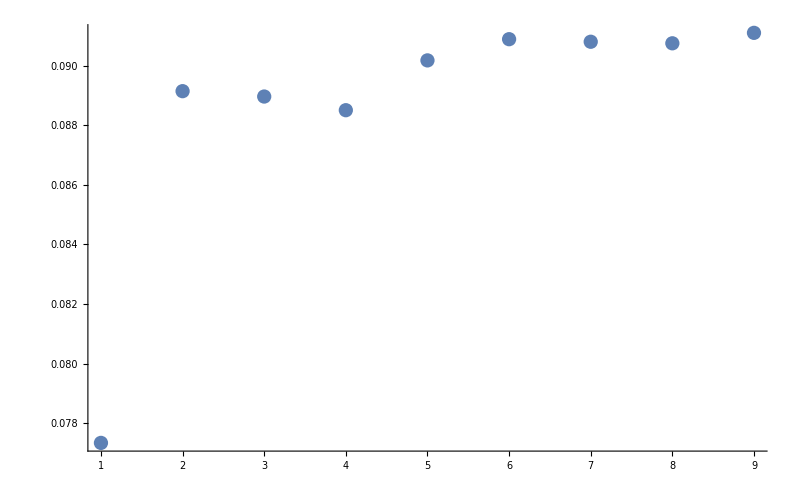
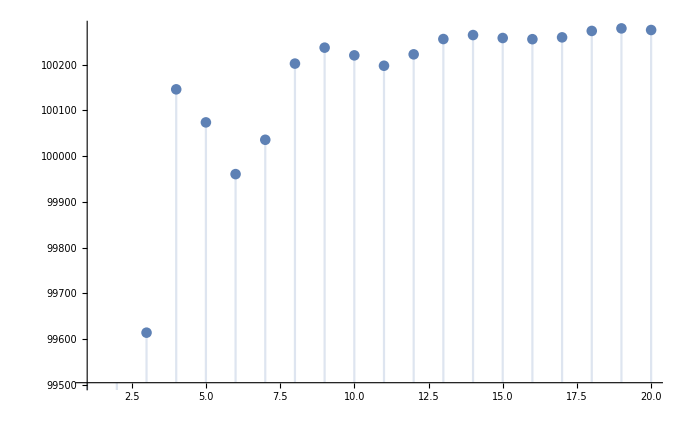
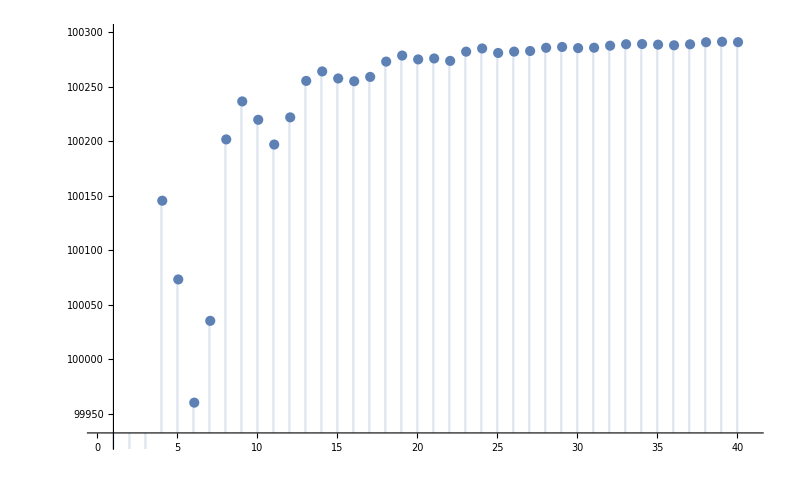
```mathematica
(* Example output of twoAnglesOptimal *)
{DateObject[{2016,8,17},TimeObject[{15,44},TimeZone->2.],TimeZone->2.],{41.80,0},7.5,8.6}

(* percentages change, first relative to the first, then to the previous *)
{0,0.0214891,0.0269413,0.0262005,0.0250416,0.025811,0.0275178,0.0278751,0.0277023}
{0,0.0214891,0.00533747,-0.000721313,-0.00112938,0.000750613,0.00166387,0.000347719,-0.000168099}

(* with -22 azimuth: *)
{0.0773427,0.0891427,0.0889624,0.088504,0.090175,0.0908864,0.0908002,0.0907483,0.0910989}
{0.0773427,0.0109529,-0.00016553,-0.000420986,0.00153513,0.000652584,-0.0000789884,-0.0000475611,0.000321402}
-Graphics--Graphics--Graphics-
```

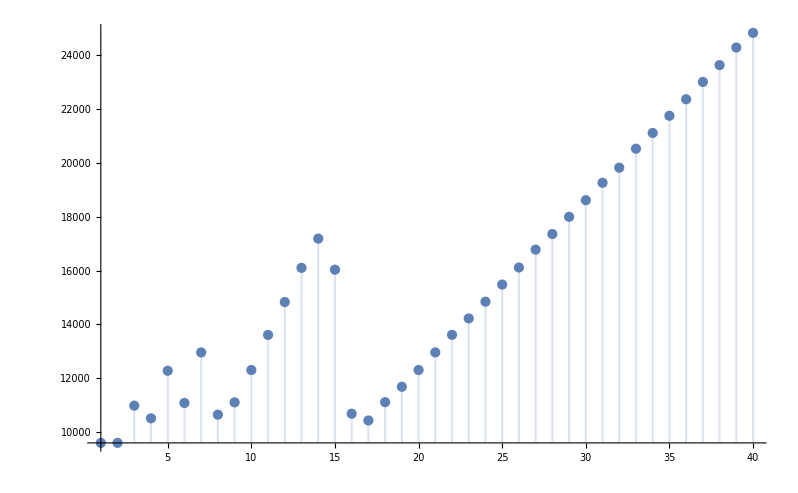
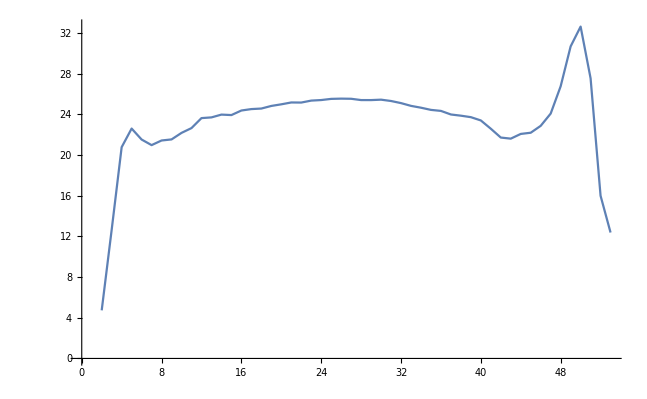
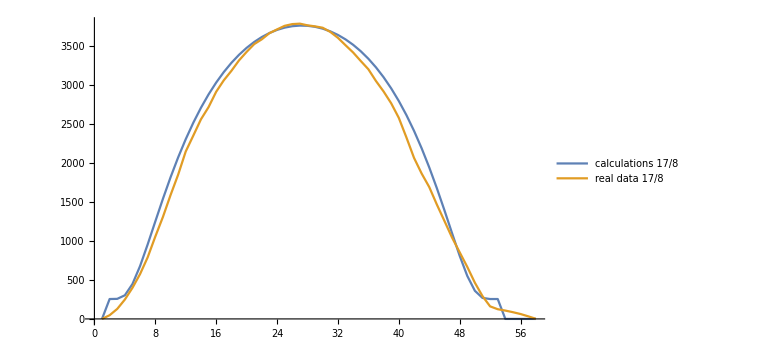
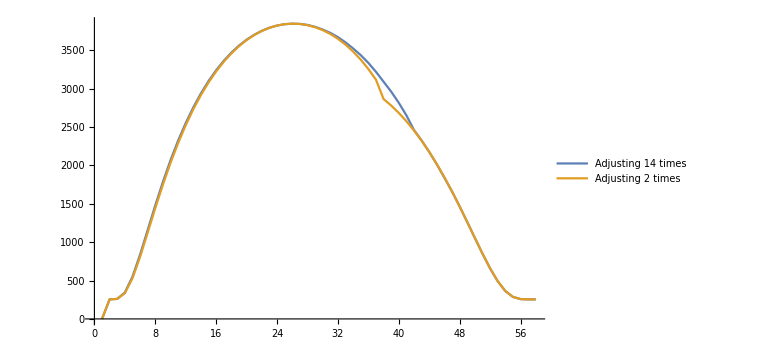
```mathematica
old -Graphics-
efficiency percentage over 17/8 -Graphics-
-Graphics-


14 times  {53.7416,51.8324,49.8813,47.5458,44.9358,42.1948,38.8167,34.4008,28.2102,18.7959,0.604448,0.,0.,0.}
-Graphics-
(* values for 2016 *)
{{"2016-01-01",78.0588},{"2016-01-02",77.9635},{"2016-01-03",77.8589},{"2016-01-04",77.7451},{"2016-01-05",78.0197},{"2016-01-06",77.8977},{"2016-01-07",77.7462},{"2016-01-08",77.5851},{"2016-01-09",77.4365},{"2016-01-10",77.2572},{"2016-01-11",77.0919},{"2016-01-12",76.9189},{"2016-01-13",76.7132},{"2016-01-14",76.5243},{"2016-01-15",76.3281},{"2016-01-16",76.1248},{"2016-01-17",75.9146},{"2016-01-18",75.6677},{"2016-01-19",75.443},{"2016-01-20",75.4006},{"2016-01-21",75.1906},{"2016-01-22",74.9373},{"2016-01-23",74.6766},{"2016-01-24",74.4085},{"2016-01-25",74.1333},{"2016-01-26",73.8892},{"2016-01-27",73.6009},{"2016-01-28",73.306},{"2016-01-29",73.045},{"2016-01-30",72.7602},{"2016-01-31",72.4926},{"2016-02-01",72.1737},{"2016-02-02",71.8946},{"2016-02-03",71.563},{"2016-02-04",71.2722},{"2016-02-05",70.9282},{"2016-02-06",70.6258},{"2016-02-07",70.318},{"2016-02-08",69.9562},{"2016-02-09",69.6376},{"2016-02-10",69.3142},{"2016-02-11",68.9863},{"2016-02-12",68.6542},{"2016-02-13",68.2663},{"2016-02-14",67.9257},{"2016-02-15",67.5814},{"2016-02-16",67.2332},{"2016-02-17",66.8808},{"2016-02-18",66.5239},{"2016-02-19",66.162},{"2016-02-20",65.7948},{"2016-02-21",65.4222},{"2016-02-22",65.0441},{"2016-02-23",64.6605},{"2016-02-24",64.2715},{"2016-02-25",63.8777},{"2016-02-26",63.4792},{"2016-02-27",63.1329},{"2016-02-28",62.7276},{"2016-02-29",62.3193},{"2016-03-01",61.9082},{"2016-03-02",61.4936},{"2016-03-03",61.0747},{"2016-03-04",60.6506},{"2016-03-05",60.2771},{"2016-03-06",59.837},{"2016-03-07",59.3885},{"2016-03-08",58.9314},{"2016-03-09",58.5158},{"2016-03-10",58.0419},{"2016-03-11",57.5617},{"2016-03-12",57.0763},{"2016-03-13",56.6348},{"2016-03-14",56.1422},{"2016-03-15",55.6467},{"2016-03-16",55.1471},{"2016-03-17",54.686},{"2016-03-18",54.1668},{"2016-03-19",53.635},{"2016-03-20",53.0896},{"2016-03-21",51.4032},{"2016-03-22",51.9812},{"2016-03-23",51.3979},{"2016-03-24",50.8248},{"2016-03-25",50.2321},{"2016-03-26",49.64},{"2016-03-27",49.0493},{"2016-03-28",48.4712},{"2016-03-29",47.8705},{"2016-03-30",47.2584},{"2016-03-31",46.6289},{"2016-04-01",45.9892},{"2016-04-02",45.345},{"2016-04-03",44.7026},{"2016-04-04",44.0632},{"2016-04-05",43.4469},{"2016-04-06",42.8466},{"2016-04-07",42.2582},{"2016-04-08",41.6795},{"2016-04-09",41.0836},{"2016-04-10",40.4762},{"2016-04-11",39.8594},{"2016-04-12",39.239},{"2016-04-13",38.6187},{"2016-04-14",38.0172},{"2016-04-15",37.4334},{"2016-04-16",36.8644},{"2016-04-17",36.2997},{"2016-04-18",35.7271},{"2016-04-19",35.1404},{"2016-04-20",34.5416},{"2016-04-21",33.9306},{"2016-04-22",33.3381},{"2016-04-23",32.7652},{"2016-04-24",32.2159},{"2016-04-25",31.6835},{"2016-04-26",31.1522},{"2016-04-27",28.7392},{"2016-04-28",29.8049},{"2016-04-29",29.4846},{"2016-04-30",28.9151},{"2016-05-01",28.3578},{"2016-05-02",27.8239},{"2016-05-03",27.3157},{"2016-05-04",26.8208},{"2016-05-05",26.321},{"2016-05-06",25.0016},{"2016-05-07",25.2831},{"2016-05-08",24.7522},{"2016-05-09",24.2364},{"2016-05-10",23.734},{"2016-05-11",23.2612},{"2016-05-12",22.8028},{"2016-05-13",22.3585},{"2016-05-14",21.9042},{"2016-05-15",21.4425},{"2016-05-16",20.9764},{"2016-05-17",20.5077},{"2016-05-18",20.0569},{"2016-05-19",19.6266},{"2016-05-20",19.2189},{"2016-05-21",18.8269},{"2016-05-22",18.4435},{"2016-05-23",18.0649},{"2016-05-24",17.6787},{"2016-05-25",17.2927},{"2016-05-26",16.9113},{"2016-05-27",16.5408},{"2016-05-28",16.187},{"2016-05-29",15.8539},{"2016-05-30",15.5416},{"2016-05-31",15.2465},{"2016-06-01",14.9581},{"2016-06-02",14.6852},{"2016-06-03",14.4187},{"2016-06-04",14.1576},{"2016-06-05",13.9066},{"2016-06-06",13.6628},{"2016-06-07",13.4359},{"2016-06-08",13.2178},{"2016-06-09",13.0208},{"2016-06-10",12.8399},{"2016-06-11",12.6732},{"2016-06-12",12.5267},{"2016-06-13",12.3971},{"2016-06-14",12.2841},{"2016-06-15",12.1877},{"2016-06-16",12.1079},{"2016-06-17",12.0445},{"2016-06-18",11.9974},{"2016-06-19",11.9667},{"2016-06-20",11.9522},{"2016-06-21",11.954},{"2016-06-22",11.9719},{"2016-06-23",12.0023},{"2016-06-24",12.0525},{"2016-06-25",12.1188},{"2016-06-26",12.1984},{"2016-06-27",12.2968},{"2016-06-28",12.4103},{"2016-06-29",12.541},{"2016-06-30",12.6893},{"2016-07-01",12.8559},{"2016-07-02",13.0357},{"2016-07-03",13.2363},{"2016-07-04",13.4528},{"2016-07-05",13.6831},{"2016-07-06",13.925},{"2016-07-07",14.1421},{"2016-07-08",14.3912},{"2016-07-09",14.7014},{"2016-07-10",14.9748},{"2016-07-11",15.2576},{"2016-07-12",15.5531},{"2016-07-13",15.8647},{"2016-07-14",16.1953},{"2016-07-15",16.5449},{"2016-07-16",16.9111},{"2016-07-17",17.2941},{"2016-07-18",17.6766},{"2016-07-19",18.0602},{"2016-07-20",18.4375},{"2016-07-21",18.8187},{"2016-07-22",19.2069},{"2016-07-23",19.6051},{"2016-07-24",20.0296},{"2016-07-25",20.4728},{"2016-07-26",20.9359},{"2016-07-27",21.3989},{"2016-07-28",21.8604},{"2016-07-29",22.3129},{"2016-07-30",22.7535},{"2016-07-31",23.2043},{"2016-08-01",23.6654},{"2016-08-02",24.1525},{"2016-08-03",24.6645},{"2016-08-04",25.1823},{"2016-08-05",25.4266},{"2016-08-06",26.2187},{"2016-08-07",26.7163},{"2016-08-08",27.2109},{"2016-08-09",27.7038},{"2016-08-10",28.2199},{"2016-08-11",28.7587},{"2016-08-12",29.319},{"2016-08-13",29.8787},{"2016-08-14",29.1247},{"2016-08-15",30.984},{"2016-08-16",31.5115},{"2016-08-17",32.0309},{"2016-08-18",32.5679},{"2016-08-19",33.1211},{"2016-08-20",33.6945},{"2016-08-21",34.2879},{"2016-08-22",34.8863},{"2016-08-23",35.4718},{"2016-08-24",36.0474},{"2016-08-25",36.6119},{"2016-08-26",37.1657},{"2016-08-27",37.7286},{"2016-08-28",38.3115},{"2016-08-29",38.9116},{"2016-08-30",39.5183},{"2016-08-31",39.8472},{"2016-09-01",40.7402},{"2016-09-02",41.3359},{"2016-09-03",41.9161},{"2016-09-04",42.4964},{"2016-09-05",43.0713},{"2016-09-06",43.6634},{"2016-09-07",44.2728},{"2016-09-08",44.901},{"2016-09-09",45.5298},{"2016-09-10",46.1701},{"2016-09-11",46.802},{"2016-09-12",47.4182},{"2016-09-13",48.0191},{"2016-09-14",48.6142},{"2016-09-15",49.1895},{"2016-09-16",49.761},{"2016-09-17",50.3492},{"2016-09-18",50.9221},{"2016-09-19",51.5087},{"2016-09-20",52.0723},{"2016-09-21",51.2006},{"2016-09-22",53.1866},{"2016-09-23",53.7072},{"2016-09-24",54.2467},{"2016-09-25",54.7341},{"2016-09-26",55.2062},{"2016-09-27",55.717},{"2016-09-28",56.1752},{"2016-09-29",56.6309},{"2016-09-30",57.132},{"2016-10-01",57.5822},{"2016-10-02",58.0757},{"2016-10-03",58.5157},{"2016-10-04",58.9481},{"2016-10-05",59.4237},{"2016-10-06",59.8398},{"2016-10-07",60.2462},{"2016-10-08",60.7013},{"2016-10-09",61.0926},{"2016-10-10",61.4779},{"2016-10-11",61.9185},{"2016-10-12",62.2972},{"2016-10-13",62.6745},{"2016-10-14",63.1073},{"2016-10-15",63.4811},{"2016-10-16",63.853},{"2016-10-17",64.2224},{"2016-10-18",64.6426},{"2016-10-19",65.0048},{"2016-10-20",65.3631},{"2016-10-21",65.7171},{"2016-10-22",66.1215},{"2016-10-23",66.4676},{"2016-10-24",66.81},{"2016-10-25",67.2032},{"2016-10-26",67.5391},{"2016-10-27",67.8724},{"2016-10-28",68.2035},{"2016-10-29",68.5325},{"2016-10-30",68.9097},{"2016-10-31",69.233},{"2016-11-01",69.5537},{"2016-11-02",69.8711},{"2016-11-03",70.2331},{"2016-11-04",70.5428},{"2016-11-05",70.8485},{"2016-11-06",71.15},{"2016-11-07",71.494},{"2016-11-08",71.7864},{"2016-11-09",72.0745},{"2016-11-10",72.358},{"2016-11-11",72.6821},{"2016-11-12",72.9563},{"2016-11-13",73.2039},{"2016-11-14",73.4732},{"2016-11-15",73.7762},{"2016-11-16",74.0358},{"2016-11-17",74.2906},{"2016-11-18",74.5765},{"2016-11-19",74.82},{"2016-11-20",75.0577},{"2016-11-21",75.3245},{"2016-11-22",75.5493},{"2016-11-23",75.5621},{"2016-11-24",75.7998},{"2016-11-25",76.0023},{"2016-11-26",76.2267},{"2016-11-27",76.4173},{"2016-11-28",76.6273},{"2016-11-29",76.805},{"2016-11-30",77.},{"2016-12-01",77.1638},{"2016-12-02",77.3428},{"2016-12-03",77.5133},{"2016-12-04",77.6541},{"2016-12-05",77.8076},{"2016-12-06",77.9521},{"2016-12-07",78.0875},{"2016-12-08",77.8015},{"2016-12-09",77.8875},{"2016-12-10",77.987},{"2016-12-11",78.0775},{"2016-12-12",78.1589},{"2016-12-13",78.2312},{"2016-12-14",78.3134},{"2016-12-15",78.3667},{"2016-12-16",78.4105},{"2016-12-17",78.4449},{"2016-12-18",78.4698},{"2016-12-19",78.5027},{"2016-12-20",78.508},{"2016-12-21",78.5212},{"2016-12-22",78.5067},{"2016-12-23",78.5002},{"2016-12-24",78.4659},{"2016-12-25",78.4396},{"2016-12-26",78.4037},{"2016-12-27",78.3582},{"2016-12-28",78.3031},{"2016-12-29",78.2188},{"2016-12-30",78.1443},{"2016-12-31",78.0602},{"2017-01-01",78.0588}}
```